Task 1, graph 3

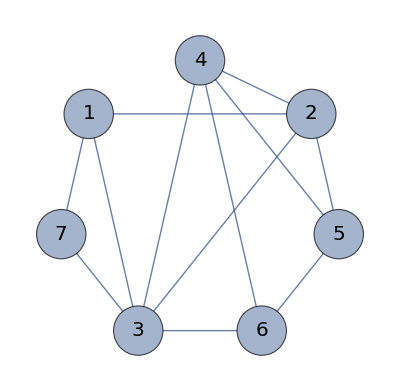

```mathematica
IndividualGraph = Graph[{1->7, 2->1,3->1,4->2,5->2,6->5,7->3, 2->3,3->6,4->3,4->5,4->6}, EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.05],VertexSize->Large,
VertexLabels->Placed["Name",Center], VertexLabelStyle->Directive[Black,Italic,20], GraphLayout->"CircularEmbedding"]
```

Task 2

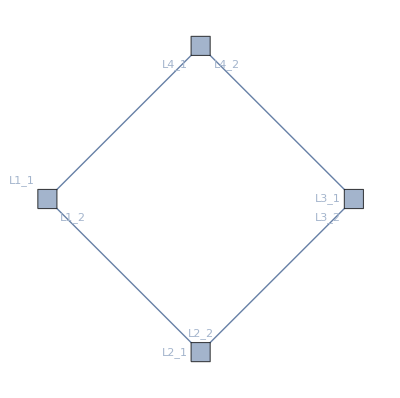

```mathematica
g2 = Graph[{1<->4,1<->2,2<->3,4<->3}, VertexShapeFunction->"Square", VertexSize->Small, VertexLabels->{
1->Placed[{"L1_1", "L1_2"},{{Above, Before},{Below, After}}],
2-> Placed[{"L2_1","L2_2"},{Before, Above}], 
3->Placed[{"L3_1", "L3_2"},{Before, {Before, Below}}],
4->Placed[{"L4_1", "L4_2"},{{Before, Below}, {After, Below}}]}]
```

Task 3

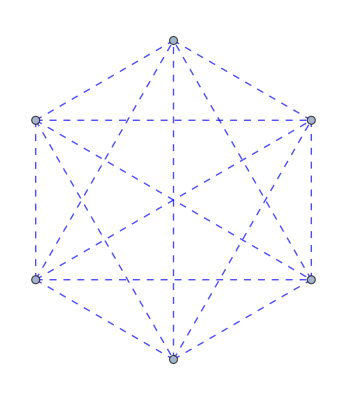
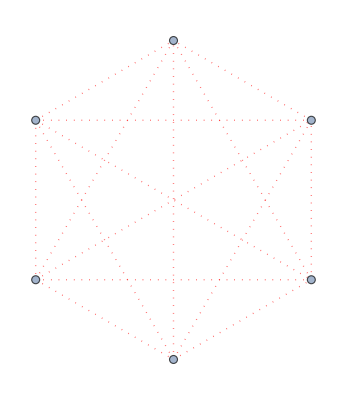
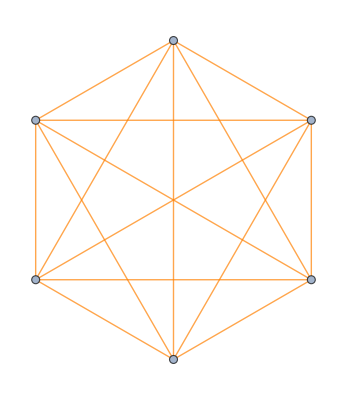

```mathematica
Table[CompleteGraph[6, VertexSize->Tiny, EdgeStyle->style], {style, {Directive[Blue, Dashed], Directive[Red,Dotted], Orange}}]
```

Task 4

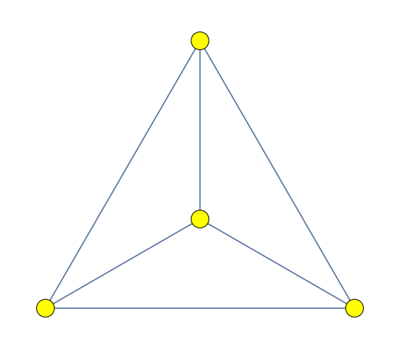
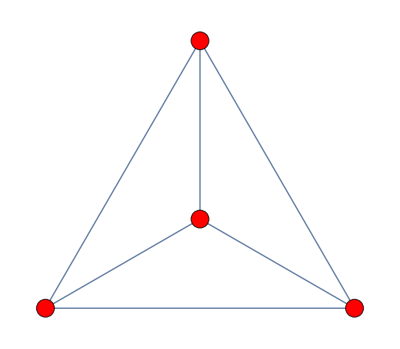
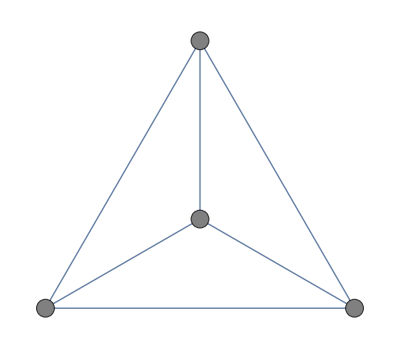

```mathematica
Table[CompleteGraph[4, VertexSize->Small, VertexStyle->vStyle], {vStyle, {Yellow, Red, Gray}}]
```

Task 5

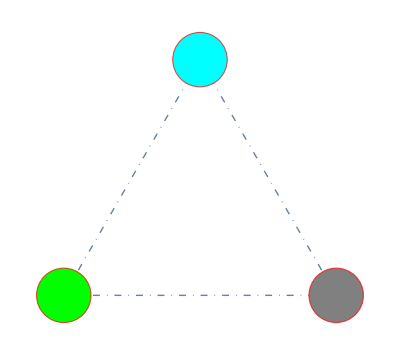
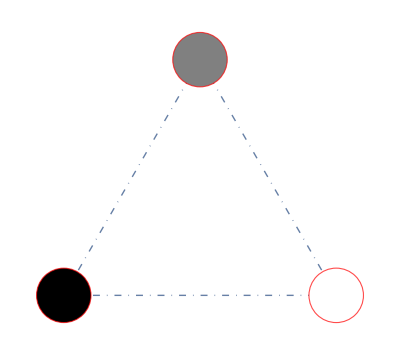
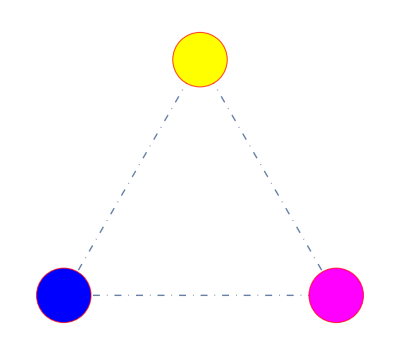

```mathematica
Table[CompleteGraph[3, EdgeStyle->DotDashed, BaseStyle->Directive[EdgeForm[Red], EdgeForm[Thick]], VertexSize->Medium, VertexStyle->vStyles], {vStyles,{ {1-> Green,2-> Gray, 3-> Cyan},{1->Black, 2->White, 3-> Gray}, {1-> Blue, 2-> Magenta, 3-> Yellow}}}]
```

Task 6

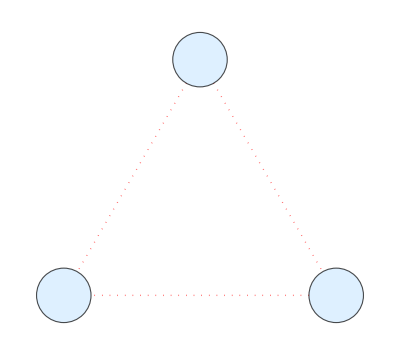
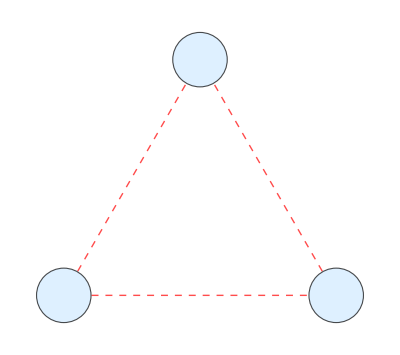
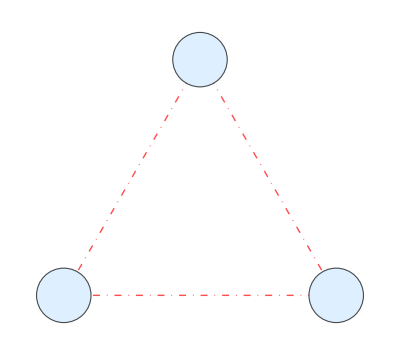

```mathematica
Table[CompleteGraph[3, VertexStyle->LightBlue, BaseStyle->Directive[Red, lineStyles, EdgeForm[lineStyles]], VertexSize->Medium],{lineStyles, {Dotted, Dashed, DotDashed}}]
```

Task 7

```mathematica
(*picture = Import["C:\\Users\\Vitaly\\Desktop\\wolframCatMeme.jpg"]*)
g7 = Graph[{4->5, 5->2,3->4, 3->1},VertexSize->0.3, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Blue,Italic,20], VertexStyle->White,VertexShape->{4->picture},GraphLayout->{"LayeredEmbedding", "RootVertex"->4}]
```

-Graphics-

Task 8

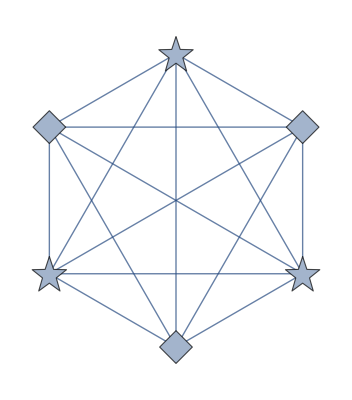

```mathematica
CompleteGraph[6,VertexShapeFunction->{_?EvenQ->"Star","Diamond"}, VertexSize->Medium]
```

Task 9

{1<->2,1<->3,1<->4,6<->7,2<->5,3<->5,3<->7,4<->6,5<->6}

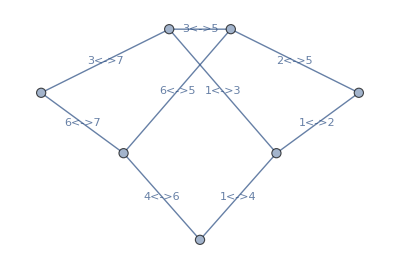

```mathematica
g9 ={1<->2, 1<->3, 1<->4, 6<->7, 2<->5, 3<->5,3<->7,4<->6,5<->6}
Graph[g9,VertexSize->0.15,EdgeLabels->"Name", GraphLayout->"HighDimensionalEmbedding"]
```

Task 10

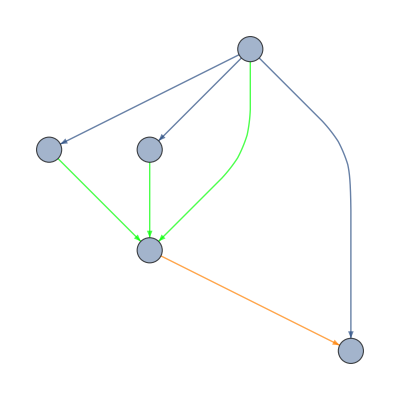

```mathematica
Graph[{1->2,1->3,1->4,1->5,3->5,4->5,5->2}, VertexLabels->Placed["Name",Center],VertexSize->0.25,
EdgeStyle->{_->5-> Green, 5->_-> Orange}]
```

Task 11

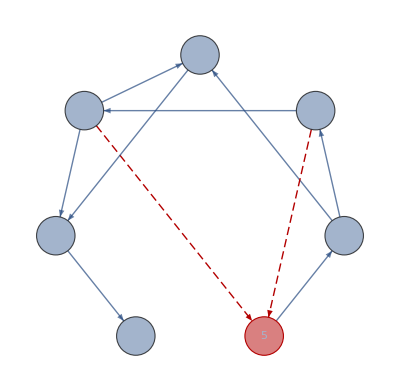

```mathematica
Graph[{1->6,1->5,1->4,2->3,3->5,2->6,6->4,5->2,3->1,4->7},VertexLabels->Placed["Name", Center],VertexSize->0.3, GraphLayout->"CircularEmbedding", GraphHighlightStyle->"Dashed", GraphHighlight->{5, _->5}]
```

Task 12

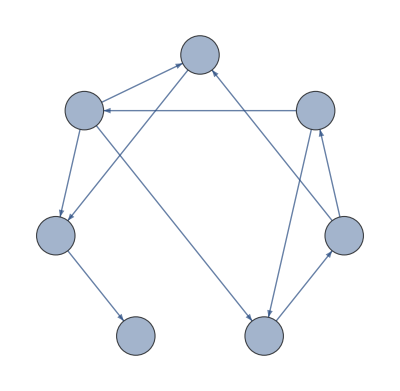

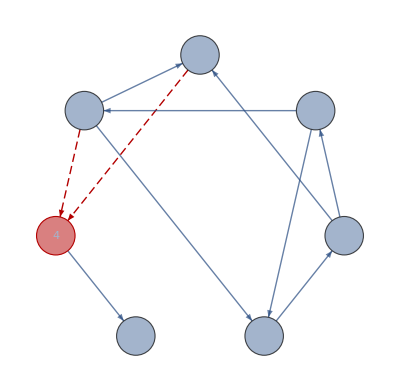

```mathematica
g12 = Graph[{1->6,1->5,1->4,2->3,3->5,2->6,6->4,5->2,3->1,4->7},VertexLabels->Placed["Name", Center],VertexSize->0.3, GraphLayout->"CircularEmbedding", GraphHighlightStyle->"Dashed"]
HighlightGraph[g12, {4, _->4}]
```